```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
(*Calcula as funçoes de forma de triângulos e quadrláteros definidas no elemento mestre*)
Compute2DShape[order_,eltype_]:=Block[{ζ1,ζ2,ζ3,a,b,xi,eta,psis,dpsis},
If[eltype==1,
If[order==1,
psis={1/4(1-xi)(1-eta),1/4(1+xi)(1-eta),1/4 (1+xi)(1+eta),1/4(1-xi)(1+eta)};
,
psis={xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,
-eta(xi+1)(xi-1)(eta-1)/2,-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,
-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)};
];
,
ζ1=1-xi-eta;
ζ2=xi;
ζ3=eta;
If[order==1,
psis={ζ1,ζ2, ζ3};
,
psis={2*ζ1*(ζ1-1/2),2*ζ2*(ζ2-1/2),2*ζ3*(ζ3-1/2),4*ζ1*ζ2,4*ζ2*ζ3,4*ζ3*ζ1};
];

];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]];
{psis,dpsis}
];
```

```mathematica
(*Retorna os pontos e os pesos da regra de integração  - order = ordem polinomial das funções de base  eltype = 1 quadrilátero 2 triângulo*)
IntegrationRule[order_,eltype_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},

If[eltype==1,
If[order==1,
matpsts={{-0.5773502691896257,0.5773502691896257,1.},{0.5773502691896257,0.5773502691896257,1.},{-0.5773502691896257,-0.5773502691896257,1.},{0.5773502691896257,-0.5773502691896257,1.}};
];
If[order==2,
matpsts={{-0.7745966692414834,0.7745966692414834,0.30864197530864174},{0.,0.7745966692414834,0.4938271604938271},{0.7745966692414834,0.7745966692414834,0.30864197530864174},{-0.7745966692414834,0.,0.4938271604938271},{0.,0.,0.7901234567901237},{0.7745966692414834,0.,0.4938271604938271},{-0.7745966692414834,-0.7745966692414834,0.30864197530864174},{0.,-0.7745966692414834,0.4938271604938271},{0.7745966692414834,-0.7745966692414834,0.30864197530864174}};
];
,
If[order==1,
matpsts=N[{{1/3,1/3,1/2}}];
];
If[order==2,
matpsts=N[{{1/6,1/6,1/2 1/3},{2/3,1/6,1/2 1/3},{1/6,2/3,1/2 1/3}}];
];

If[order==3,
matpsts=N[{{1/3,1/3,-27/48 1/2},{1/5,1/5,25/48 1/2},{1/5,3/5,25/48 1/2},{3/5,1/5,25/48 1/2}}];
];

];
matpsts//N
]
```

```mathematica
(*Calcula as funções de transformação*)
ComputeData[coords_,psis_,gradpsi_]:=Block[{x=0,y=0,Jac},

Jac=Table[0,{2},{2}];
Table[
x+=psis[[i]]coords[[i]][[1]];
y+=psis[[i]]coords[[i]][[2]];
Jac[[1,1]]+=gradpsi[[1,i]]coords[[i]][[1]];
Jac[[2,1]]+=gradpsi[[2,i]]coords[[i]][[1]];
Jac[[1,2]]+=gradpsi[[1,i]]coords[[i]][[2]];
Jac[[2,2]]+=gradpsi[[2,i]]coords[[i]][[2]];
,{i,1,Length[psis]}
];
{psis,gradpsi,Jac,x,y}
]
```

```mathematica
(*Calcula a contribuição de cada ponto de integração na matriz de rigidez do elemento*)
Contribute[data_,weight_,order_]:=Block[{f,C,fu,InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},
f[x_]:=0;
{psi,GradPsi,Jac,x,y}=data;
nnodes=Length[psi] ;
DetJ=Jac[[1,1]] Jac[[2,2]]-Jac[[2,1]] Jac[[1,2]];
InvJac={{Jac[[2,2]],-Jac[[1,2]]},{-Jac[[2,1]],Jac[[1,1]]}}/DetJ;
GradPhi=InvJac.GradPsi;
C=Table[0,{3},{3}];
nusqr=nu nu;
C[[1,1]]=young/(1-nusqr);C[[2,2]]=young/(1-nusqr);C[[1,2]]=nu young/(1-nusqr);
C[[2,1]]=nu young/(1-nusqr);C[[3,3]]=young/(2 (1+nu));
wpLocal=weight  DetJ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

fu=-1;
Table[
ef[[2i+fu]] += psi[[i]]wpLocal f[x];
ef[[(2i+1+fu)]]+=psi[[i]] wpLocal f[x];
Table[
ek[[2 i+fu,2j+fu]]+=h( GradPhi[[1,i]] C[[1,1]]  GradPhi[[1,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[2,j]])wpLocal  ;
ek[[2 i+fu,2j+1+fu]]+=h( GradPhi[[1,i]] C[[1,2]]  GradPhi[[2,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
ek[[2 i+1+fu,2j+fu]]+=h( GradPhi[[2,i]] C[[1,2]]  GradPhi[[1,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+1+fu,2j+1+fu]]+=h( GradPhi[[2,i]] C[[2,2]]  GradPhi[[2,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
,{j,1, nnodes}];
,{i,1, nnodes}];

{ek,ef}
]
```

```mathematica
(*Calcula a matriz de rigidez de cada elemento*)
CalcStiff[order_,elcoords_,eltype_]:=Block[{nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts},

nnodes=Length[elcoords];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
intrule=IntegrationRule[order,eltype];
{psis,GradPsi}=Compute2DShape[order,eltype];
npts=Length[intrule];
Table[
{xi,eta,w}=intrule[[i]];
data=ComputeData[elcoords,psis,GradPsi];
{ek,ef}+=Contribute[data,w,order];
,{i,1,npts}];
{ek,ef}
]
```

```mathematica
(*Realiza a montagem da matriz de rigidez global*)
Assemble[allcoords_,nnodes_,topol_,order_,eltype_]:=Block[{nels,rows,sz,cols,Kglob,Fglob,co,Ke,Fe,fu,rowglob,colglob},
nels=Length[allcoords];
rows=Length[allcoords[[1]]] ;
sz= 2 Length[nnodes];
cols=rows;
Kglob=Table[0,{ sz},{ sz}];
Fglob=Table[0,{sz}];
Table[
co=allcoords[[k]]//N;
{Ke,Fe}=CalcStiff[order,co,eltype];
fu=-1;
Table[
rowglob=topol[[k,i]];
Table[
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];
,{j,1,cols}];
Fglob[[2rowglob+fu]]+=Fe[[i]];
,{i,1,rows}];
,{k,1,nels}];
{Kglob,Fglob}
]
```

```mathematica
(*Calcula funçoes de forma 1D*)
ComputeShape[order_,var_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
ListPoli[npoints]
]
```

```mathematica
(*Encontra todos os ids e coordenadas entre os ids especificados*)
FindLineElemens[id1_,id2_,nnodes_,order_]:=Block[{h1,h2,allids,Flag,A,B,tol,i,ids,nodesvec,linenodes,temp1,temp2,elsvec,idsvec,nodes,newout,norm},
A=nnodes[[id1]];
B=nnodes[[id2]];
tol=10^-3;
linenodes={};
ids={};
nodesvec={};
elsvec={};
Flag=True;
h1=Sqrt[A[[1]]A[[1]]+A[[2]]A[[2]]];
h2=Sqrt[B[[1]]B[[1]]+B[[2]]B[[2]]];
For[i=1,i≤Length[nnodes],i++,
(*Vertical Line*)
If[Abs[A[[1]]-B[[1]]]<tol && Abs[nnodes[[i]][[1]]-A[[1]]]<tol,
If[Between[nnodes[[i]][[2]],{{A[[2]],B[[2]]},{B[[2]],A[[2]]}}],
AppendTo[linenodes,{nnodes[[i]],i}];
];
Flag=False;
,
(*Horizontal Line*)
If[Abs[A[[2]]-B[[2]]]<tol&& Abs[nnodes[[i]][[2]]-A[[2]]]<tol,
If[Between[nnodes[[i]][[1]],{{A[[1]],B[[1]]},{B[[1]],A[[1]]}}],
AppendTo[linenodes,{nnodes[[i]],i}];

];
Flag=False;
,
norm=Norm[nnodes[[i]]];
If[(Abs[norm-h1])<tol&&Abs[norm-h2]<tol  &&Flag≠False,
AppendTo[linenodes,{nnodes[[i]],i}];
 ];
];
];
];
newout=Transpose[SortBy[linenodes,Smaller]];
allids=newout[[2]];
nodes={};
ids={};
idsvec={};
nodesvec={};
Table[
AppendTo[nodes,newout[[1,i]]];
AppendTo[ids,newout[[2,i]]];
If[Length[ids]==order+1,
AppendTo[nodesvec,nodes];
AppendTo[idsvec,ids];
temp1=ids[[order+1]];
temp2=nodes[[order+1]];
nodes={};
ids={};
AppendTo[ids,temp1];
AppendTo[nodes,temp2];
];
,{i,1,Length[linenodes]}];
{nodesvec,idsvec,allids}
];
```

```mathematica
(*Aplica condição de contorno de dirichlet em uma linha definida por dois ids*)
ContributeLineDirichlet[EK_,EF_,nodes_,id1_,id2_,ek_,ef_,order_]:=Block[{nodevec,idsvec,x1,x2,y1,y2,Ef=EF,Ek=EK,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,k},
{nodevec,idsvec,ids}=FindLineElemens[id1,id2,nodes,order];
idsd2=ids;
el=Length[ids];
For[i=1,i≤el,i++,
For[j=1,j≤2,j++,
For[k=1,k≤2,k++,
Ek[[2ids[[i]] +j-2,2ids[[i]]+k-2 ]]*=ek[[j,k]];
];
Ef[[2ids[[i]] +j-2]]=ef[[j]];
];
];
{Ek,Ef}
];
```

```mathematica
(*Calcula a normal*)
ComputeNormalDirection[p1_,p2_]:=Block[{cos,sin},
cos=(p1[[1]]-p2[[1]])/Sqrt[(p1[[1]]-p2[[1]])^2 +(p1[[2]]-p2[[2]])^2];
sin=(p1[[2]]-p2[[2]])/Sqrt[(p1[[1]]-p2[[1]])^2 +(p1[[2]]-p2[[2]])^2];
{-sin,cos}
];
(*Calcula o vetor de cargas considerando a condição de contorno de Newmann*)
ContributeLineNewman[EF_,fx_,nodes_,order_,id1_,id2_]:=Block[{vecnodes,idsvec,ids,normal,coordinates,temp=0,co,el,i,shapes,xi,x0,y0,xf,yf,h,cos,sin,vertOrHor,x,J,vecPtosPesos,xix,w,integral,Ef=EF},

{vecnodes,idsvec,ids}=FindLineElemens[id1,id2,nodes,order];
el=Length[vecnodes];
shapes=ComputeShape[order,xi];
For[i=1,i≤el,i++,
coordinates=Table[0,{order+1}];
co=vecnodes[[i]];
x0=co[[1,1]];
xf=co[[Length[co],1]];
y0=co[[1,2]];
yf=co[[Length[co],2]];
h=Sqrt[(xf-x0)^2 +(yf-y0)^2];
cos=(xf-x0)/h;
sin=(yf-y0)/h;
temp=0;
Table[
coordinates[[k]]=temp;
temp+=h/order;
,{k,1,order+1}
];
x=Sum[shapes[[i]] coordinates[[i]],{i,1,order+1}];
J=D[x,xi];
vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integral=Table[Sum[((fx[co[[j]]]shapes[[j]]J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];
Table[
If[j≠order+1,
normal=ComputeNormalDirection[vecnodes[[i]][[j]],vecnodes[[i]][[j+1]]];
];
Ef[[ idsvec[[i,j]] 2-1]]+=integral[[j]]normal[[1]];
Ef[[ idsvec[[i,j]] 2]]+=integral[[j]]normal[[2]];
,{j,1,order+1}];
];
Ef
];
```

```mathematica
ComputeNormals[pt_]:=Block[{lines,x,delta,intdata,R=300,normal,v},
Clear[r];
rr[x_]=-x/(√(R^2-0.999999999999999 x^2));

pervec[v_]:={-v[[2]]/Norm[v],v[[1]]/Norm[v]};
lines=rr[pt[[1]]](x-pt[[1]])+ pt[[2]];
delta=10^-8;
normal=({pt[[1]]+delta,lines/.x->pt[[1]]+delta}-{pt[[1]],lines/.x->pt[[1]]})/Norm[({pt[[1]]+delta,lines/.x->pt[[1]]+delta}-{pt[[1]],lines/.x->pt[[1]]})];
pervec[normal]
]
```

```mathematica
(*Calcula o vetor de cargas considerando a condição de contorno de Newmann*)
ContributeLineNewmanPressure[EF_,fx_,nodes_,order_,id1_,id2_]:=Block[{vecnodes,idsvec,ids,normal,coordinates,temp=0,co,el,i,shapes,xi,x0,y0,xf,yf,h,cos,sin,vertOrHor,x,J,vecPtosPesos,xix,w,integral,Ef=EF},
sumx=0.;
sumy=0.;
{vecnodes,idsvec,ids}=FindLineElemens[id1,id2,nodes,order];
vecdata=vecnodes;
(*Print["id1 = ",id1];
Print["id2 = ",id2];
Print["vecnodes = ",vecnodes];*)
el=Length[vecnodes];
shapes=ComputeShape[order,xi];
For[i=1,i≤el,i++,
coordinates=Table[0,{order+1}];
co=vecnodes[[i]];
x0=co[[1,1]];
xf=co[[Length[co],1]];
y0=co[[1,2]];
yf=co[[Length[co],2]];
h=Sqrt[(xf-x0)^2 +(yf-y0)^2];
cos=(xf-x0)/h;
sin=(yf-y0)/h;
temp=0;
Table[
coordinates[[k]]=temp;
temp+=h/order;
,{k,1,order+1}
];
(*teste=ComputeNormals[co];*)
x=Sum[shapes[[i]] coordinates[[i]],{i,1,order+1}];
J=D[x,xi];
vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integral=Table[Sum[((fx[co[[j]]]shapes[[j]]J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];
Table[
normal=ComputeNormals[vecnodes[[i]][[j]]];
Ef[[ idsvec[[i,j]] 2-1]]+=integral[[j]]normal[[1]];
Ef[[ idsvec[[i,j]] 2]]+=integral[[j]]normal[[2]];
,{j,1,order+1}];
];
Ef
];
```

```mathematica
(*Dada uma coordenada de nó encontra o correspondente id*)
FindIds[nodes_,coords_]:=Block[{nodestofind=Nearest[nodes,coords][[All,1]]},Flatten[Position[nodes,Alternatives@@nodestofind]]]
```

```mathematica
(*Calcula a solução e a derivada definida em cada elemento*)
ComputeSol[topol_,coords_,order_,coefs_,eltype_]:=Block[{X,InvJ,GradPhi,GradPsi,nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},
{psis,GradPsi}=Compute2DShape[order,eltype];
nels=Length[topol];
sol=Table[0,{nels},{2}];
X=Table[0,{nels},{2}];
dsol=Table[0,{nels},{4}];
Table[
x=0.;
y=0.;
kk=Length[psis];
Table[
id=topol[[i,j]];
x+=coords[[id,1]] psis[[j]];
y+=coords[[id,2]] psis[[j]];
,{j,1,kk}];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
DetJac=Det[Jac];
InvJ=Inverse[Jac];
GradPhi=InvJ.GradPsi;
Table[
id=topol[[i,j]];
sol[[i,1]]+=(psis[[j]] coefs[[2 id-1]] );
sol[[i,2]]+=(psis[[j]] coefs[[2id]] );
(*duxdx*)
dsol[[i,1]]+=(GradPhi[[1,j]]coefs[[2 id-1]] );
(*duxdy*)
dsol[[i,2]]+=(GradPhi[[2,j]] coefs[[2id-1]] );
(*duydx*)
dsol[[i,3]]+=(GradPhi[[1,j]]coefs[[2id]] );
(*duydy*)
dsol[[i,4]]+=(GradPhi[[2,j]] coefs[[2id]] );
,{j,1,kk}];
X[[i,1]]=x;
X[[i,2]]=y;
,{i,1,nels}];
{sol,dsol,X}
]
```

```mathematica
(*Calcula as tensões e deformações nos elementos*)
ComputeStress[dsol_,young_,nu_]:=Block[{strain,gradu,lambda=young nu/((1+nu)(1-2 nu)),mu=young/(2(1+nu)),dudx,dudy,dvdx,dvdy,i,eps,stress,ex,ey,exy,C},

strain=Table[0,{Length[dsol]}];
stress=Table[0,{Length[dsol]}];
For[i=1,i≤Length[dsol],i++,

{dudx,dudy,dvdx,dvdy}=dsol[[i]];
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
strain={ex,ey,exy};
(*If[i==1,Print["{dudx,dudy,dvdx,dvdy} = ",{dudx,dudy,dvdx,dvdy}]];*)
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
stress[[i]]=C.strain;
(*gradu={{dudx,dudy},{dvdx,dvdy}};
eps[[i]]=(gradu+Transpose[gradu])/2;
stress[[i]]=lambda Tr[eps[[i]]]IdentityMatrix[2]+2 mu eps[[i]];*)

];
{stress,strain}
];
```

```mathematica
(*Função de auxílio ao pós-processamento*)
computesollist[X_,sols_,sx_]:=Block[{refine,sollists,v,x,y,s,sollist},
sollists={};
refine=1/3.;
v=Table[{xi,eta},{xi,0,1,refine},{eta,1-xi,0,refine}];

refine=1/2.;
v=Table[{xi,eta},{xi,-1,1,refine},{eta,-1,1,refine}];
sollists=Table[0,{Length[X]}];
Table[
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
sollists[[i]]=sollist;
,{i,1,Length[X]}];
sollists
]
```

{{{2,1},{5,2},{4,6},{1,4}}}

{{1,2,3,4}}

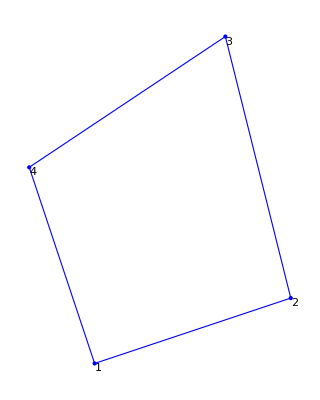

Element Stiffness Matrix = (0.407005 | 0.104972 | -0.300742 | -0.139621 | -0.0902343 | -0.115496 | -0.0160288 | 0.150145
0.104972 | 0.545515 | -0.0729543 | -0.0286192 | -0.115496 | -0.277013 | 0.0834783 | -0.239883
-0.300742 | -0.0729543 | 0.702964 | -0.142679 | 0.0518507 | 0.0812231 | -0.454073 | 0.13441
-0.139621 | -0.0286192 | -0.142679 | 0.393915 | 0.14789 | -0.182347 | 0.13441 | -0.182949
-0.0902343 | -0.115496 | 0.0518507 | 0.14789 | 0.316499 | 0.107979 | -0.278116 | -0.140373
-0.115496 | -0.277013 | 0.0812231 | -0.182347 | 0.107979 | 0.4688 | -0.073706 | -0.00944048
-0.0160288 | 0.0834783 | -0.454073 | 0.13441 | -0.278116 | -0.073706 | 0.748217 | -0.144182
0.150145 | -0.239883 | 0.13441 | -0.182949 | -0.140373 | -0.00944048 | -0.144182 | 0.432273)

```mathematica
h=1;
order=1;
young=1;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{2,1},{5,2},{4,6},{1,4}}}
topol={{1,2,3,4}}
eltype=1;
forcing=0.;
nnodes={{2,1},{5,2},{4,6},{1,4}};
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis]
{kE,fE}=Assemble[allcoords,nnodes,topol,order,eltype];
Print["Element Stiffness Matrix = ",MatrixForm[kE]]
```

{{{0,0},{0.5,0.5},{0.3,1}}}

{{1,2,3}}

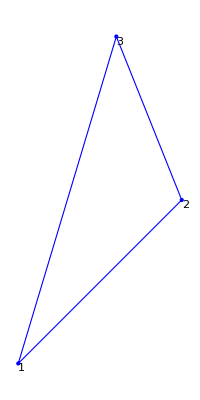

Element Stiffness Matrix = (0.40381 | 0.0952381 | -0.727619 | -0.0571429 | 0.32381 | -0.0380952
0.0952381 | 0.20381 | 0.00952381 | -0.194286 | -0.104762 | -0.00952381
-0.727619 | 0.00952381 | 1.57524 | -0.285714 | -0.847619 | 0.27619
-0.0571429 | -0.194286 | -0.285714 | 0.708571 | 0.342857 | -0.514286
0.32381 | -0.104762 | -0.847619 | 0.342857 | 0.52381 | -0.238095
-0.0380952 | -0.00952381 | 0.27619 | -0.514286 | -0.238095 | 0.52381)

```mathematica
h=1;
order=1;
young=1;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{0,0},{0.5,0.5},{0.3,1}}}
topol={{1,2,3}}
eltype=2;
forcing=0.;
nnodes={{0,0},{0.5,0.5},{0.3,1}};
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis]
{kE,fE}=Assemble[allcoords,nnodes,topol,order,eltype];
Print["Element Stiffness Matrix = ",MatrixForm[kE]]
```

Element Stiffness Matrix = (0.300523 | 0.0641471 | -0.00406102 | 0.00580932 | -0.0182484 | -0.0186238 | -0.0705443 | -0.0164129 | -0.297688 | -0.0188103 | 0.0479151 | 0.0673114 | 0.0616122 | 0.0673114 | 0.0146412 | 0.0700785 | -0.0341501 | -0.220811
0.0641471 | 0.300523 | -0.0164129 | -0.0705443 | -0.0186238 | -0.0182484 | 0.00580932 | -0.00406102 | 0.0700785 | 0.0146412 | 0.0673114 | 0.0616122 | 0.0673114 | 0.0479151 | -0.0188103 | -0.297688 | -0.220811 | -0.0341501
-0.00406102 | -0.0164129 | 0.380042 | -0.140819 | -0.0570223 | 0.0216762 | -0.0182484 | 0.0191023 | -0.278482 | 0.147235 | -0.022493 | -0.155006 | 0.0603432 | -0.0682683 | 0.0929883 | -0.0826742 | -0.153066 | 0.275166
0.00580932 | -0.0705443 | -0.140819 | 0.558468 | -0.000545998 | 0.0256815 | 0.0191023 | -0.0182484 | 0.0583465 | -0.00179537 | -0.0661171 | -0.324008 | -0.0682683 | 0.0473381 | -0.0826742 | 0.160754 | 0.275166 | -0.377645
-0.0182484 | -0.0186238 | -0.0570223 | -0.000545998 | 0.776433 | 0.333284 | 0.0256815 | 0.0216762 | 0.159485 | 0.0817172 | -0.018749 | 0.00552764 | -0.371132 | -0.0833613 | 0.0924113 | 0.0817172 | -0.588859 | -0.421391
-0.0186238 | -0.0182484 | 0.0216762 | 0.0256815 | 0.333284 | 0.776433 | -0.000545998 | -0.0570223 | 0.0817172 | 0.0924113 | -0.0833613 | -0.371132 | 0.00552764 | -0.018749 | 0.0817172 | 0.159485 | -0.421391 | -0.588859
-0.0705443 | 0.00580932 | -0.0182484 | 0.0191023 | 0.0256815 | -0.000545998 | 0.558468 | -0.140819 | 0.160754 | -0.0826742 | 0.0473381 | -0.0682683 | -0.324008 | -0.0661171 | -0.00179537 | 0.0583465 | -0.377645 | 0.275166
-0.0164129 | -0.00406102 | 0.0191023 | -0.0182484 | 0.0216762 | -0.0570223 | -0.140819 | 0.380042 | -0.0826742 | 0.0929883 | -0.0682683 | 0.0603432 | -0.155006 | -0.022493 | 0.147235 | -0.278482 | 0.275166 | -0.153066
-0.297688 | 0.0700785 | -0.278482 | 0.0583465 | 0.159485 | 0.0817172 | 0.160754 | -0.0826742 | 1.55088 | -0.188714 | -0.376261 | -0.274477 | -0.123815 | -0.00382787 | -0.592551 | 0.42453 | -0.202317 | -0.0849787
-0.0188103 | 0.0146412 | 0.147235 | -0.00179537 | 0.0817172 | 0.0924113 | -0.0826742 | 0.0929883 | -0.188714 | 1.80586 | -0.274477 | -0.15445 | -0.00382787 | 0.101332 | 0.42453 | -0.592551 | -0.0849787 | -1.35844
0.0479151 | 0.0673114 | -0.022493 | -0.0661171 | -0.018749 | -0.0833613 | 0.0473381 | -0.0682683 | -0.376261 | -0.274477 | 1.58951 | 0.104501 | -0.0304582 | 0.22395 | 0.101332 | -0.00382787 | -1.33813 | 0.10029
0.0673114 | 0.0616122 | -0.155006 | -0.324008 | 0.00552764 | -0.371132 | -0.0682683 | 0.0603432 | -0.274477 | -0.15445 | 0.104501 | 1.075 | 0.22395 | -0.0304582 | -0.00382787 | -0.123815 | 0.10029 | -0.193086
0.0616122 | 0.0673114 | 0.0603432 | -0.0682683 | -0.371132 | 0.00552764 | -0.324008 | -0.155006 | -0.123815 | -0.00382787 | -0.0304582 | 0.22395 | 1.075 | 0.104501 | -0.15445 | -0.274477 | -0.193086 | 0.10029
0.0673114 | 0.0479151 | -0.0682683 | 0.0473381 | -0.0833613 | -0.018749 | -0.0661171 | -0.022493 | -0.00382787 | 0.101332 | 0.22395 | -0.0304582 | 0.104501 | 1.58951 | -0.274477 | -0.376261 | 0.10029 | -1.33813
0.0146412 | -0.0188103 | 0.0929883 | -0.0826742 | 0.0924113 | 0.0817172 | -0.00179537 | 0.147235 | -0.592551 | 0.42453 | 0.101332 | -0.00382787 | -0.15445 | -0.274477 | 1.80586 | -0.188714 | -1.35844 | -0.0849787
0.0700785 | -0.297688 | -0.0826742 | 0.160754 | 0.0817172 | 0.159485 | 0.0583465 | -0.278482 | 0.42453 | -0.592551 | -0.00382787 | -0.123815 | -0.274477 | -0.376261 | -0.188714 | 1.55088 | -0.0849787 | -0.202317
-0.0341501 | -0.220811 | -0.153066 | 0.275166 | -0.588859 | -0.421391 | -0.377645 | 0.275166 | -0.202317 | -0.0849787 | -1.33813 | 0.10029 | -0.193086 | 0.10029 | -1.35844 | -0.0849787 | 4.24569 | 0.0612459
-0.220811 | -0.0341501 | 0.275166 | -0.377645 | -0.421391 | -0.588859 | 0.275166 | -0.153066 | -0.0849787 | -1.35844 | 0.10029 | -0.193086 | 0.10029 | -1.33813 | -0.0849787 | -0.202317 | 0.0612459 | 4.24569)

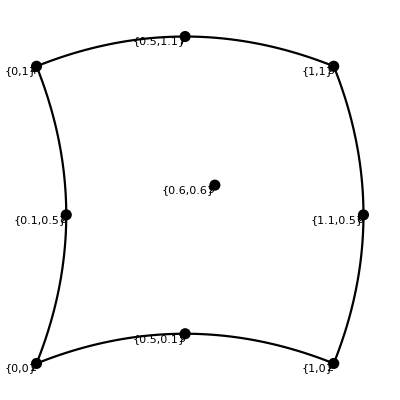

```mathematica
h=1;
order=2;
young=1;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{0,0},{1,0},{1,1},{0,1},{0.5,0.1},{1.1,0.5},{0.5,1.1},{0.1,0.5},{0.6,0.6}}};
nnodes=Flatten[allcoords,1];
topol={{1,2,3,4,5,6,7,8,9}};
forcing=0.;
eltype=1;
{kE,fE}=Assemble[allcoords,nnodes,topol,order,eltype];
Print["Element Stiffness Matrix = ",MatrixForm[kE]]
Clear[x,y]
xcurves=Fit[allcoords[[1,#]],{1,x,x^2},x]&/@{{1,5,2},{4,7,3}};
ycurves=Fit[Reverse/@allcoords[[1,#]],{1,y,y^2},y]&/@{{1,8,4},{2,6,3}};
sh=Show[Graphics[{PointSize[0.02],Point/@allcoords}],Plot[xcurves,{x,0,1},PlotStyle->Black],ContourPlot[{x==First@ycurves,x==Last@ycurves},{x,0,1.2},{y,0,1},ContourStyle->Black]];
nnodes=Flatten[allcoords,1];
nodeVis2=Graphics[{MapIndexed[Text[#2[[1]],#1,{2,2}]&,nnodes],{Black,Point[nnodes]}}];
nodeVis3=Graphics[{MapIndexed[Text[#1,#1,{1.5,4}]&,nnodes],{Black,Point[nnodes]}}];
defelp2=Show[nodeVis3,nodeVis2,sh]
```

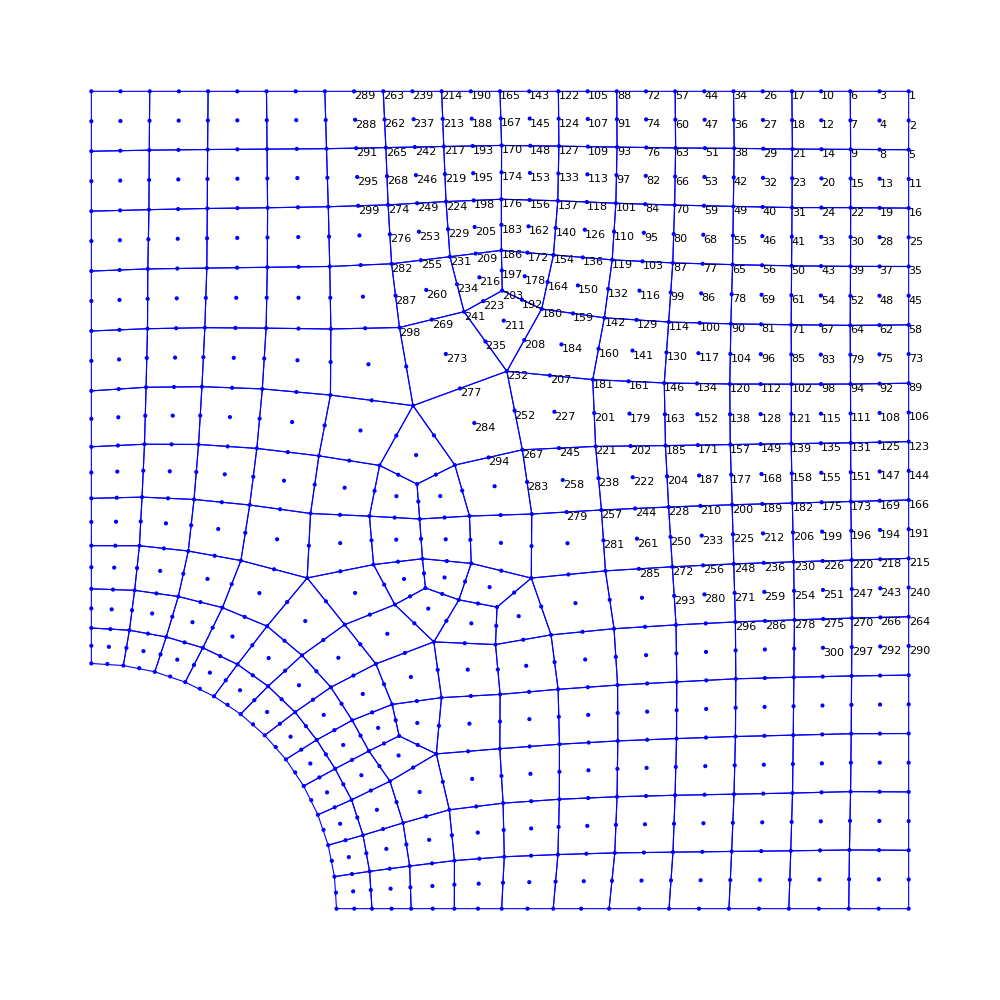

-Graphics-

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\Miscellaneous\\elschapacomfuroleft.txt","Table"],1];
nnodesAll=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\Miscellaneous\\noschapacomfuroleft.txt","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,9}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
mesh=Show[meshVis1,nodeVis,ImageSize->1000]
h=1;
order=2;
eltype=1;
forcing=0.;
young=205000;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
eltype=1;
(*AbsoluteTiming[Assemble[allcoords,topol,order,forcing,eltype];]*)
{KE,FE}=Assemble[allcoords,nnodes,topol,order,eltype];
matrix=MatrixPlot[KE,ImageSize->Large]
```

```mathematica
1000/14.
```

71.4286

```mathematica
71 71.42857142857143
```

5071.43

```mathematica
nodetofind={{300,0},{0,300}};
{hole1,hole2}=FindIds[nnodes,nodetofind]
nodetofind={{300,0},{1000,0}};
{inferiorline1,inferiorline2}=FindIds[nnodes,nodetofind]
nodetofind={{0,300},{0,1000}};
{leftline1,leftline2}=FindIds[nnodes,nodetofind]
```

{870,871}

{644,870}

{645,871}

-5995.72

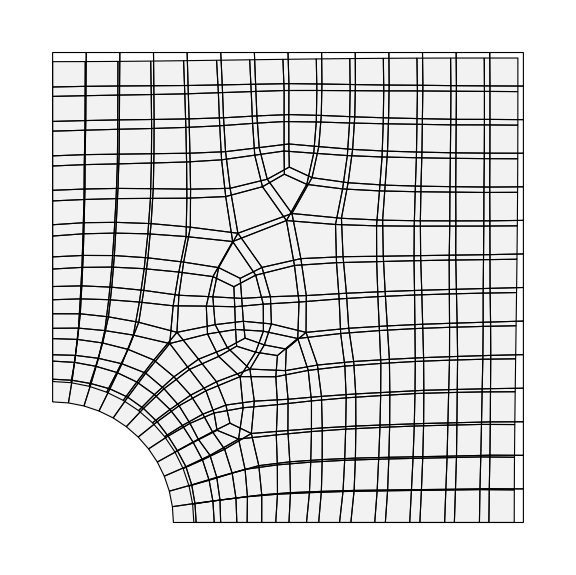

```mathematica
FE=Table[0,{Length[KE]}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,inferiorline1,inferiorline2,{{1,1},{1,10^12}},{0,0},order];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,leftline1,leftline2,{{10^12,1},{1,1}},{0,0},order];
f[pt_]:=-10;
(*FE=ContributeLineNewman[FE,f,nnodes,order,hole1,hole2];*)
FE=ContributeLineNewmanPressure[FE,f,nnodes,order,hole2,hole1];
Sum[FE[[i]],{i,1,Length[FE]}]
sol=LinearSolve[KE,FE,Method->"Banded"];
scale=2000;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVis1=Graphics[{FaceForm[],EdgeForm[{Dashed}],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
meshVisDef=Graphics[{FaceForm[{Gray,Opacity[0.1]}],EdgeForm[Black],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}];
defplussundef=Show[meshVisDef,meshVis1,ImageSize->Large]
```

```mathematica
Export["C:\\Users\\diogo\\Dropbox\\ArtigoFemMathematica - Copy\\template\\figuras\\defplussundef.png",defplussundef,ImageResolution->300]
```

C:\Users\diogo\Dropbox\ArtigoFemMathematica - Copy\template\figuras\defplussundef.png

```mathematica
{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol,eltype]//Simplify//Chop;
stress=ComputeStress[(dsols),young,nu][[1]];
```

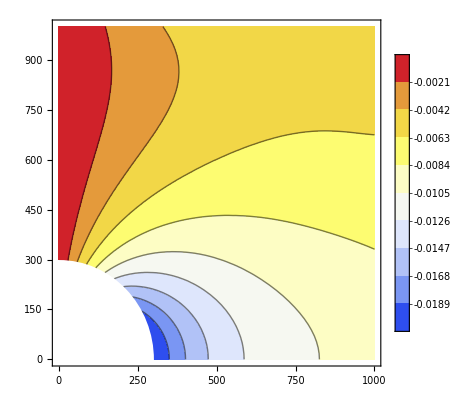

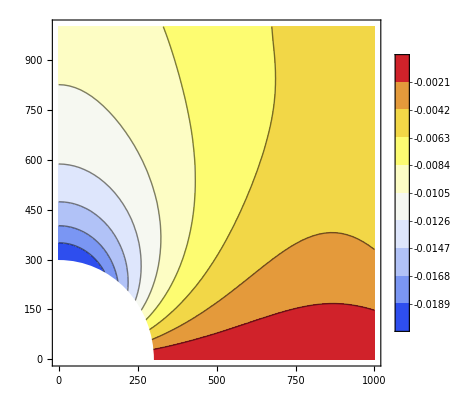

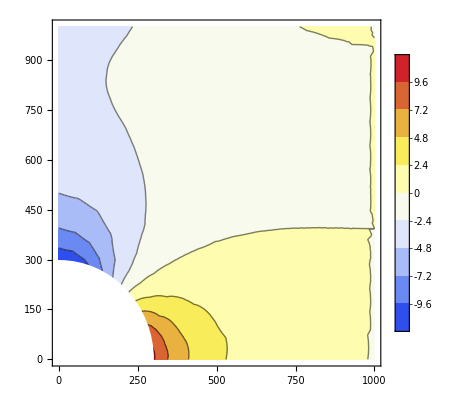

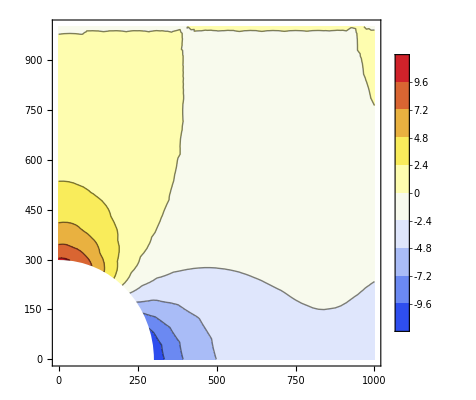

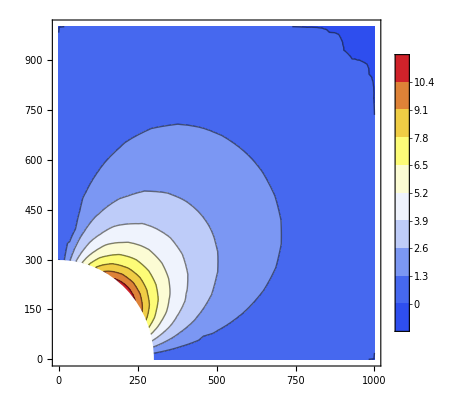

C:\Users\diogo\Dropbox\ArtigoFemMathematica - Copy\template\figuras\lpux.png

C:\Users\diogo\Dropbox\ArtigoFemMathematica - Copy\template\figuras\lpuy.png

C:\Users\diogo\Dropbox\ArtigoFemMathematica - Copy\template\figuras\lpsx.png

C:\Users\diogo\Dropbox\ArtigoFemMathematica - Copy\template\figuras\lpsy.png

C:\Users\diogo\Dropbox\ArtigoFemMathematica - Copy\template\figuras\lpsxy.png

```mathematica
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
tabux=computesollist[X,sols,1];
tabuy=computesollist[X,sols,2];
tabsx=computesollist[X,stress,1];
tabsy=computesollist[X,stress,2];
tabsxy=computesollist[X,stress,3];
lpux=ListContourPlot[Flatten[tabux,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->9];
lpuy=ListContourPlot[Flatten[tabuy,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->9];
lpsx=ListContourPlot[Flatten[tabsx,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->9,PlotRange->{-12,12}];
lpsy=ListContourPlot[Flatten[tabsy,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->9,PlotRange->{-12,12}];
lpsxy=ListContourPlot[Flatten[tabsxy,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->9,PlotRange->{-1,12}];
lpux=Show[lpux,lpd]
lpuy=Show[lpuy,lpd]
lpsx=Show[lpsx,lpd]
lpsy=Show[lpsy,lpd]
lpsxy=Show[lpsxy,lpd]

Export["C:\\Users\\diogo\\Dropbox\\ArtigoFemMathematica - Copy\\template\\figuras\\lpux.png",lpux,ImageResolution->300]
Export["C:\\Users\\diogo\\Dropbox\\ArtigoFemMathematica - Copy\\template\\figuras\\lpuy.png",lpuy,ImageResolution->300]
Export["C:\\Users\\diogo\\Dropbox\\ArtigoFemMathematica - Copy\\template\\figuras\\lpsx.png",lpsx,ImageResolution->300]
Export["C:\\Users\\diogo\\Dropbox\\ArtigoFemMathematica - Copy\\template\\figuras\\lpsy.png",lpsy,ImageResolution->300]
Export["C:\\Users\\diogo\\Dropbox\\ArtigoFemMathematica - Copy\\template\\figuras\\lpsxy.png",lpsxy,ImageResolution->300]
```

```mathematica
(*Dada a matriz de rigidez e o vetor de carga globais, aplica condição de contorno definida em nós*)
ApplyNodeBC[Kglob_,Fglob_,node_,type_,ek_,ef_]:=Block[{position,i,j,kglob=Kglob,fglob=Fglob},

If[type≠0&&type≠1 && type≠2,Print["Unknown type. Specify 0 for Dirichlet, 1 for Newman or 2 for Mixed."]];
position=node 2-1;
If[type==0,
(*Dirichlet - Specified Solution *)
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,
kglob[[position+i-1,position+j-1]]*=ek[[i,j]];
];
fglob[[position+i-1]]=ef[[i]];
];
];
If[type==1,
For[i=1,i≤2,i++,
fglob[[position+i-1]]+=ef[[i]];
];
];
{kglob,fglob}
]
```

{{{0,0},{10,0},{0,6}},{{10,0},{10,6},{0,6}}}

{{1,2,3},{2,4,3}}

{{0,0},{10,0},{0,6},{10,6}}

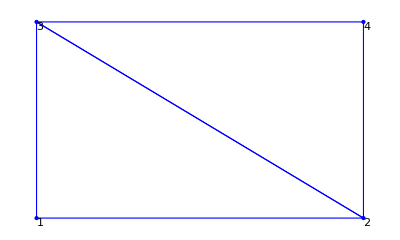

(6.50183×10^18 | 3.57143×10^6 | -3.2967×10^6 | -1.92308×10^6 | -3.20513×10^6 | -1.64835×10^6 | 0 | 0
3.57143×10^6 | 1.03114×10^19 | -1.64835×10^6 | -1.15385×10^6 | -1.92308×10^6 | -9.15751×10^6 | 0 | 0
-3.2967×10^6 | -1.64835×10^6 | 6.50183×10^6 | 0. | 0. | 3.57143×10^6 | -3.20513×10^6 | -1.92308×10^6
-1.92308×10^6 | -1.15385×10^6 | 0. | 1.03114×10^19 | 3.57143×10^6 | 0. | -1.64835×10^6 | -9.15751×10^6
-3.20513×10^6 | -1.92308×10^6 | 0. | 3.57143×10^6 | 6.50183×10^18 | 0. | -3.2967×10^6 | -1.64835×10^6
-1.64835×10^6 | -9.15751×10^6 | 3.57143×10^6 | 0. | 0. | 1.03114×10^7 | -1.92308×10^6 | -1.15385×10^6
0 | 0 | -3.20513×10^6 | -1.64835×10^6 | -3.2967×10^6 | -1.92308×10^6 | 6.50183×10^6 | 3.57143×10^6
0 | 0 | -1.92308×10^6 | -9.15751×10^6 | -1.64835×10^6 | -1.15385×10^6 | 3.57143×10^6 | 1.03114×10^7)

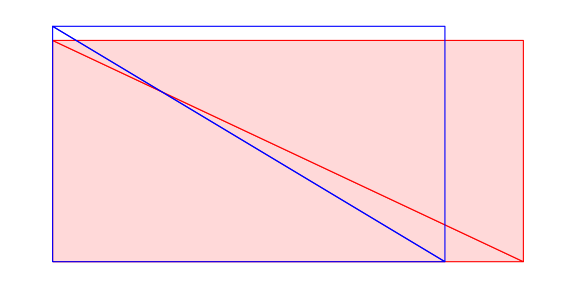

{0,0,0.002,0,0,-0.00036,0.002,-0.00036}

```mathematica
h=1;
order=1;
young=10 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{0,0},{10,0},{0,6}},{{10,0},{10,6},{0,6}}}
topol={{1,2,3},{2,4,3}}
eltype=2;
forcing=0.;
nnodes={{0,0},{10,0},{0,6},{10,6}}
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis]
(*{KE,FE}=Assemble[allcoords,topol,order,forcing,eltype];*)
{KE,FE}=Assemble[allcoords,nnodes,topol,order,eltype];
matrix=MatrixPlot[KE,ImageSize->Large];
{KE,FE}=ApplyNodeBC[KE,FE,1,0,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ApplyNodeBC[KE,FE,2,0,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ApplyNodeBC[KE,FE,3,0,{{10^12,1},{1,1}},{0,0}];
{KE,FE}=ApplyNodeBC[KE,FE,2,1,{{1,1},{1,1}},{6000,0}];
{KE,FE}=ApplyNodeBC[KE,FE,4,1,{{1,1},{1,1}},{6000,0}];
MatrixForm[KE]
sol=LinearSolve[KE,FE,Method->"Banded"];
scale=1000;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3}]]]]}];
Show[meshVisDef,meshVis1,ImageSize->Large]
sol//Chop
```

{{{0,0},{120,0},{120,160}},{{0,0},{120,160},{0,160}}}

{{1,2,3},{1,3,4}}

{{0,0},{120,0},{120,160},{0,160}}

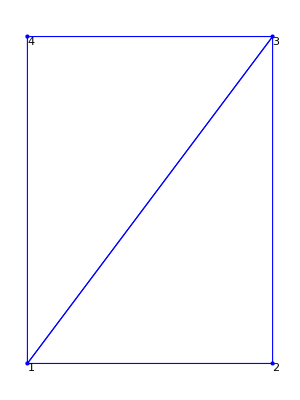

(9.3×10^17 | 0. | -768000. | 144000. | 0. | -360000. | -162000. | 216000.
0. | 7.2×10^17 | 216000. | -288000. | -360000. | 0. | 144000. | -432000.
-768000. | 216000. | 930000. | -360000. | -162000. | 144000. | 0 | 0
144000. | -288000. | -360000. | 720000. | 216000. | -432000. | 0 | 0
0. | -360000. | -162000. | 216000. | 930000. | 0. | -768000. | 144000.
-360000. | 0. | 144000. | -432000. | 0. | 720000. | 216000. | -288000.
-162000. | 144000. | 0 | 0 | -768000. | 216000. | 9.3×10^17 | -360000.
216000. | -432000. | 0 | 0 | 144000. | -288000. | -360000. | 7.2×10^17)

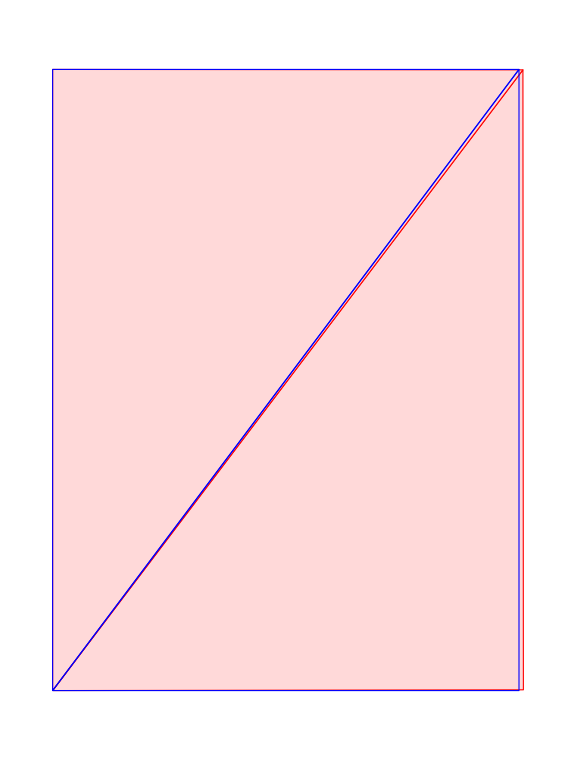

```mathematica
order=1;
h=0.036;(*inch*)
young=30 10^6;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{0,0},{120,0},{120,160}},{{0,0},{120,160},{0,160}}}(*inch*)
topol={{1,2,3},{1,3,4}}
eltype=2;
forcing=0.;
nnodes={{0,0},{120,0},{120,160},{0,160}}
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis]
(*{KE,FE}=Assemble[allcoords,topol,order,forcing,eltype];*)
{KE,FE}=Assemble[allcoords,nnodes,topol,order,eltype];
matrix=MatrixPlot[KE,ImageSize->Large];

{KE,FE}=ApplyNodeBC[KE,FE,1,0,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ApplyNodeBC[KE,FE,4,0,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ApplyNodeBC[KE,FE,2,1,{{1,1},{1,1}},{800,0}];
{KE,FE}=ApplyNodeBC[KE,FE,3,1,{{1,1},{1,1}},{800,0}];

MatrixForm[KE]
sol=LinearSolve[KE,FE,Method->"Banded"];
scale=1000;

deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3}]]]]}];
Show[meshVisDef,meshVis1,ImageSize->Large]
10^4 sol//Chop
```